## Variable internal stores (1 nutrient) + fluctuating temperature affecting μ∞

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.3 (October 4, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Aux[R]->{Equation:>a(Rin-R)-v[R]n,Color->Blue},
Pop[pop]->{
Component[Q]:>{Equation:>v[R]-μ[Q]Q,Type->"Intensive",Color->Orange},
Component[n]:>{Equation:>(μ[Q]-m)n,Color->Darker@Green}
},
Parameters:>{a>0,Rin>0,vmax>0,H>0,μ∞>0,Qmin>0,m>0},
Period:>τ
}]
```

```mathematica
v[R_]:=vmax R/(R+H);
μ[Q_]:=μ∞(1-Qmin/Q);
```

```mathematica
a=1;
Rin=10;
vmax=10;
H=1;
μ∞:=E^T; (* max growth rate is an exponential function of temperature *)
Qmin=1;
m=0.5;
```

```mathematica
T:=Tav+A Sin[2π t/τ]; (* temperature is a sinusoidal function of time *)
```

```mathematica
Tav=0;
A=2;
τ=1;
```

Dynamics starting with low abundance goes through two phases.

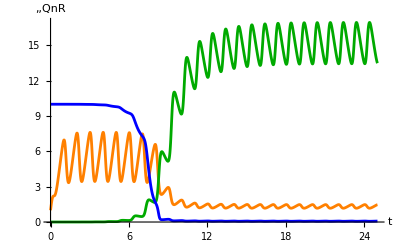

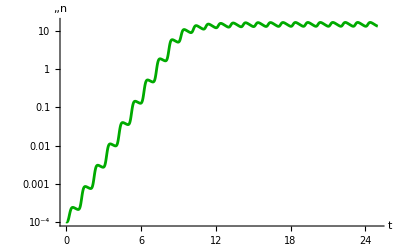

```mathematica
sol=EcoSim[{R->Rin,Q->Qmin,n->0.0001},25];
PlotDynamics[sol]
PlotDynamics[sol,{n},Logged->True]
```

The variables fluctuate over each period, but the average trend of the population is exponential growth (positive invasion fitness).    To calculate the invasion rate, we solve for the quota dynamics with no population and R=Rin:

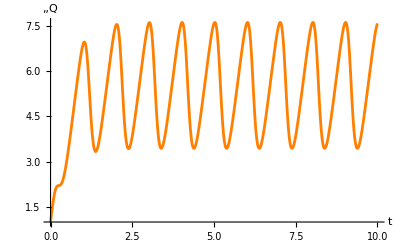

```mathematica
qsol=EcoSim[{R->Rin,Q->Qmin,n->0},10τ];
PlotDynamics[qsol,{Q}]
```

The quota reaches a stable cycle, so let's find it exactly:

Infinity::indet: Indeterminate expression -∞+∞ encountered.

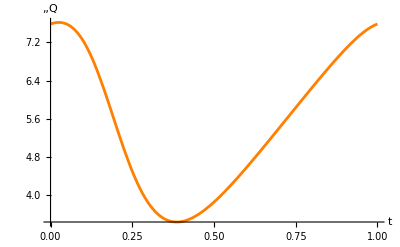

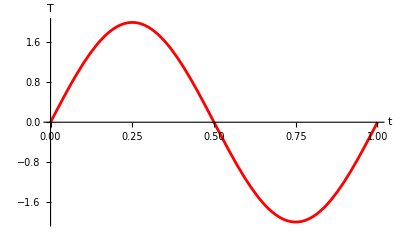

```mathematica
qec=FindEcoCycle[FinalSlice[qsol]];
PlotDynamics[qec,{Q}]
Plot[T,{t,0,τ},PlotStyle->Red,AxesLabel->{"t",Style["T",Red]}]
```

Plot instantaneous growth rate (1/N)dN/dt forced by the quota dynamics:

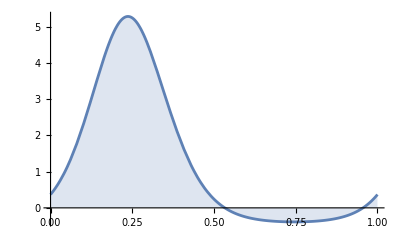

```mathematica
Plot[μ[Q[t]]-m/.qec,{t,0,τ},Filling->Axis]
```

and integrate (1/N)dN/dt over one period to calculate the invasion rate:

```mathematica
inv=NIntegrate[μ[Q[t]]-m/.qec,{t,0,τ}]/τ
```

1.28826

Comparing the invasion dynamics with our calculated rate:

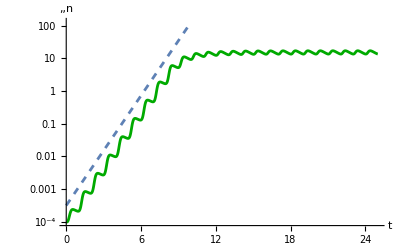

```mathematica
Show[
PlotDynamics[sol,{n},Logged->True],
LogPlot[10^(-3.5)E^(inv t),{t,0,10},PlotStyle->Dashed]
]
```

## for slides

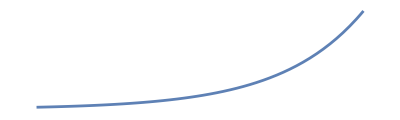

```mathematica
Plot[E^t,{t,0,4},Axes->None,AspectRatio->0.3]
```

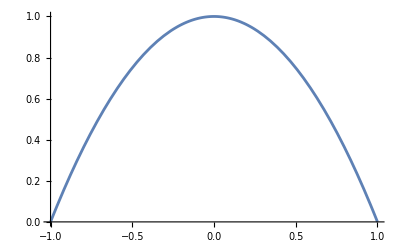

```mathematica
Plot[1-x^2,{x,-1,1},Ticks->None,AxesOrigin->{-1,0}]
```

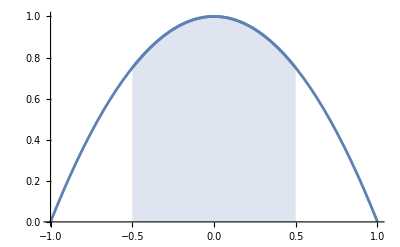

```mathematica
Show[
Plot[1-x^2,{x,-1,1},Ticks->None,AxesOrigin->{-1,0}],
Plot[1-x^2,{x,-0.5,0.5},Filling->Axis,PlotRange->{0,1}]
]
```

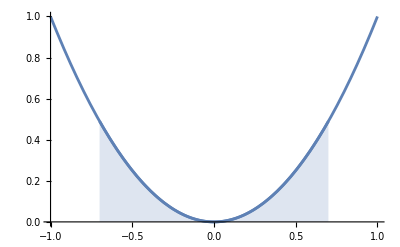

```mathematica
Show[
Plot[x^2,{x,-1,1},Ticks->None,AxesOrigin->{-1,0}],
Plot[x^2,{x,-0.7,0.7},Filling->Axis,PlotRange->{0,1}]
]
```